```mathematica
Clear["Global`*"]
```

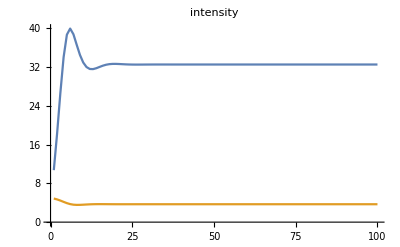

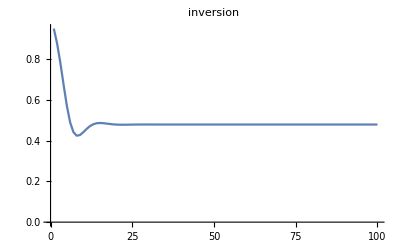

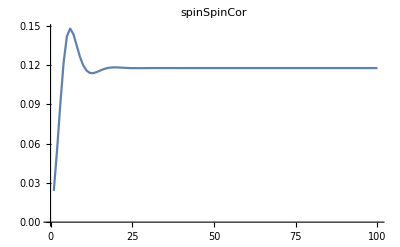

```mathematica
(*When doing one run*)
name ="N50_repumping2.5";
intensity=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
intensityUnCor=Flatten[Import[NotebookDirectory[]<>name<>"/intensityUnCor.dat"]];
inversion=Flatten[Import[NotebookDirectory[]<>name<>"/inversion.dat"]];
spinSpinCor=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCor.dat"]];
ListLinePlot[{intensity,intensityUnCor},PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversion,PlotRange->All,PlotLabel->"inversion"]
ListLinePlot[spinSpinCor,PlotRange->All,PlotLabel->"spinSpinCor"]
```